# The Hexagonal Lattice Ising Model

Simulations and Visualization of the Ising Model on a Hexagonal Lattice, through the Metropolis Algorithm .

Thiago R Bergamaschi, Jun. 24,  2018

In this notebook, I will talk about the Ising Model interaction and the Metropolis algorithm. We will observe one of the simplest and most famous examples of a phase transition, and simulate it with a intuitive, step by step algorithm.  I’ll begin with a brief introduction on the Ising Model, then I’ll develop a lattice visualization function, talk about the Metropolis algorithm, and conclude with simulations of the system and possible further explorations.

## The Ising Model

The Ising Model is a model of Ferromagnetism in Statistical mechanics. Each magnetic dipole on a lattice either points upwards or downwards, represented by +1 or -1. Their energy presents nearest-neighbor interaction terms, and, in dimensions greater than 2, presents identifiable phase transitions, as we will see. We can mathematically express the energy as follows:

E=-J∑_(<i, j>) σ_i σ_j

Where <i, j> represents a sum over nearest neighbors.

## Representation and Visualization

In this section, I will be developing visualization functions to plot our system. To start, let us look at our spin representation. I will be using a square matrix of 1’s (spin up), -1’s (spin down), and 0’s (padding). Here, let us initialize a random set of spins, padded by 0’s at the edges.

```mathematica
spinsinit[size_]:=ReplaceAll[ArrayPad[RandomInteger[{1,2}, {size, size}], 1], 2->-1]
```

The spin’s positions (i, j) can be mapped to a hexagonal lattice. We can use a table to map these representations, following simple geometrical transformations:

```mathematica
hexMap[size_]:=Table[{i Sqrt[3], j}, {i, 1, size}, {j, Mod[i, 2], 2size-1, 2}]
```

and plot their positions:

```mathematica
Graphics[{Blue,Disk[#, 1]&/@(hexMap[10]//Flatten//Partition[#, 2]&)} ];
```

To conclude this section, we need a function that will map spin values to lattice sites (ArrayPlot doesn’t exist for non-square lattices!). Let us start defining color transformation rules, for visualization purposes. Here, black will represent spin up, light gray spin down, and gray for edge padding (the borders).

```mathematica
IsingColorRules= {1->Black, -1->LightGray, 0->Gray};
```

```mathematica
v=Replace[#, IsingColorRules]&/@(spinsinit[10]//Flatten)
```

{GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0],GrayLevel[0.85],GrayLevel[0],GrayLevel[0],GrayLevel[0.85],GrayLevel[0],GrayLevel[0],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.85],GrayLevel[0],GrayLevel[0],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.85],GrayLevel[0],GrayLevel[0],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.85],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.85],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.85],GrayLevel[0],GrayLevel[0],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0],GrayLevel[0.85],GrayLevel[0],GrayLevel[0.85],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.85],GrayLevel[0],GrayLevel[0],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0.85],GrayLevel[0],GrayLevel[0],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5],GrayLevel[0.5]}

Finally, we need a plot function. To do that, let us riffle the color list and site list together, to be able to map each color to each coordinate correctly.

```mathematica
hexIsingPlot[spins_List] := Module[{size=spins//Length, sites, colors},
	sites=hexMap[size]//Flatten//Partition[#, 2]&;
	colors=Replace[#, IsingColorRules]&/@(spins//Flatten);
	Graphics[Prepend[Riffle[colors, Disk[#,1]&/@sites], AbsolutePointSize[10]]]
	]
```

Let us look at the result!

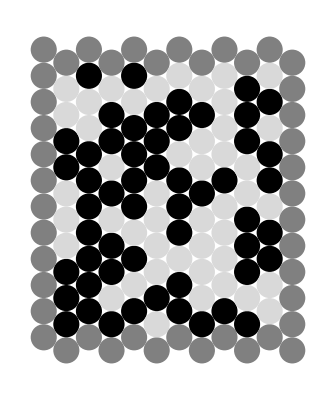

```mathematica
hexIsingPlot[spinsinit[10]]
```

## The Metropolis Algorithm

The Metropolis algorithm is essentially a Markov Chain Monte Carlo Algorithm.

First, we randomly select the indices of the lattice point we want to evolve (for intermediary visualisation, let us evaluate on a 12 by 12
 hexagonal lattice)

```mathematica
m=spinsinit[10];
```

```mathematica
{i,j}=RandomInteger[{2, Length[m]-1},2];
```

Now, lets calculate that points’ contribution to the energy. Note that we include diagonal terms to behave as a hexagonal lattice.

```mathematica
e[i_, j_,m_]:=-(m[[i-1, j]]+m[[i+1, j]]+m[[i, j-1]]+m[[i, j+1]]+m[[i-1, j-1]]+m[[i+1, j+1]])m[[i, j]]
```

Calculate the energy!

```mathematica
e[i, j, m];
```

Note that the change in energy due to a spin flip is clearly negative twice the value above. Thus, we can define a transition function, where the transition probability is defined by a Boltzmann factor.

```mathematica
transition[{i_,j_}, m_, JkT_]:=
	If[
	RandomReal[]<Exp[2 JkT e[i, j, m]],
	ReplacePart[m, {i, j}->-m[[i, j]]],
	m
	]
```

We can join the functions above into a step function, and evolve this system by successively applying it.

```mathematica
IsingStep[m_, JkT_]:=transition[RandomInteger[{2, Length[m]-1}, 2], m, JkT]
```

We can use a nested list to store these iterations, as follows:

```mathematica
IsingEvolve[m_,JkT_, steps_]:=NestList[IsingStep[#,JkT]&, m, steps]
```

Finally, we can use a manipulate to visualize the evolution of these steps. Joining everything together,

```mathematica
IsingPlot[size_, JkT_, steps_, samplerate_]:=
 ListAnimate[hexIsingPlot[First[#]]&/@Partition[IsingEvolve[spinsinit[size], JkT, steps], samplerate]]
```

Let’s simulate it! Play around with the animation below, and see what happens as the steps increase. Be careful with the sample rate, the code is very memory intensive!

```mathematica
IsingPlot[60, 5, 50000, 1000]
```

After playing about for a bit, what do we notice? Well, compare the plots at different temperatures, for a given random initialization:

High Temperature:

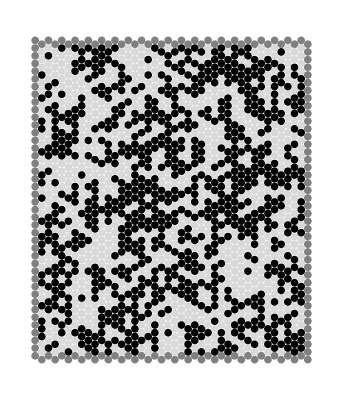

```mathematica
m0=spinsinit[40];
hexIsingPlot[IsingEvolve[m0, .1, 100000][[100000]]]
```

Low Temperature:

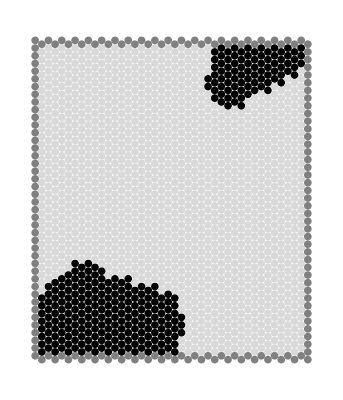

```mathematica
m0=spinsinit[40];
hexIsingPlot[IsingEvolve[m0, 5, 100000][[100000]]]
```

One clusters, the other doesn’t! Clearly, we have a phase transition. 
At low enough temperatures (high JkT) the system gradually transitions to an ordered phase. In a finite size, finite step simulation, we observe patches of spins of same state: the clusters we see above. At high temperatures, the system is in a disordered phase: Flip transitions are always extremely likely, so no clusters can ever form (and remain stable).

## Further explorations

Analysis of further geometries and lattice types

Analysis of critical temperatures for the set of different lattices

## Author contact information

tigbergamaschi@gmail.com

thiagob@mit.edu